## CellOutwardVector-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 13:59:25
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 13:48:55
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

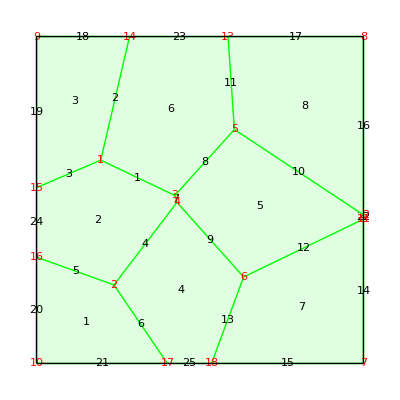

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

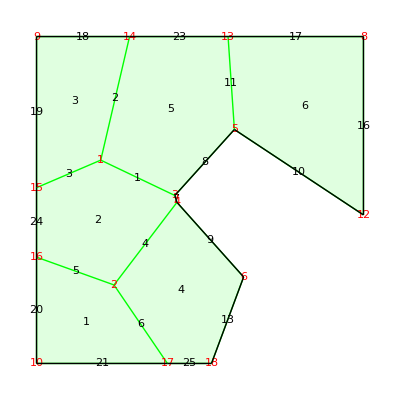

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
map=ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

## Find the outward vectors from each vertex in cell 4

```mathematica
CellVertexNumbers[S,4]
```

{17,18,6,4,2}

```mathematica
COV=CellOutwardVector[S,4,#]&/@CellVertexNumbers[S,4]
```

{{-0.187238,-0.982315},{0.380509,-0.924777},{0.978076,0.208248},{-0.0501732,0.998741},{-0.996915,0.0784874}}

```mathematica
CVC=CellVertexCoordinates[S,4]
```

{{-9.96816,-50.},{3.51364,-50.},{13.3465,-23.5523},{-7.05082,-0.717519},{-26.3031,-25.9855}}

#### figure out a good number for the length of the vector

```mathematica
len = .5 * EdgeLengths[S]//Mean
```

15.5212

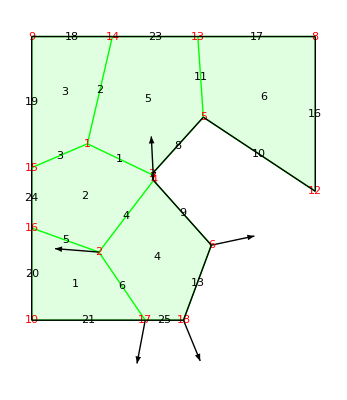

```mathematica
Show[map,Graphics[MapThread[Arrow[{#1,#1+len*#2}]&, {CVC, COV}]]]
```

## Generate a non-convex cell from the boundary and illustrate how the function may fail to generate truly outward-pointing vectors (at all vertices) in this situation.

```mathematica
bcw=BoundaryCell[S]
```

{Coordinates→{{-7.69439,1.38307},{-7.05082,-0.717519},{13.3465,-23.5523},{3.51364,-50.},{-9.96816,-50.},{-50,-50},{-50.,-17.4795},{-50.,3.77083},{-50,50},{-21.5404,50.},{8.58309,50.},{50,50},{50.,-4.56473},{10.5236,21.5665}},Edges→{7,9,13,25,21,20,24,19,18,23,17,16,10,8},Vertices→{3,4,6,18,17,10,16,15,9,14,13,8,12,5}}

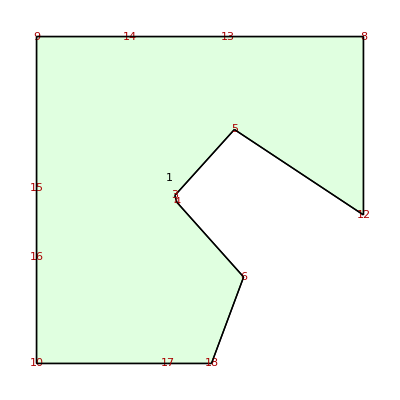

```mathematica
TPrime=Tissue[TissueVertices[S], TissueEdges[S], {"Edges"/.bcw}];
cellmap=ShowTissue[TPrime, "VertexNumbers"-> True, "CellNumbers"-> True]
```

```mathematica
COV=CellOutwardVector[TPrime,1,#]&/@CellVertexNumbers[TPrime,1]
```

{{0.31147,-0.950256},{0.306306,-0.951933},{0.601086,-0.799184},{0.22279,-0.974867},{-0.00894288,-0.99996},{-0.581132,-0.81381},{-0.858175,-0.513357},{-0.997273,-0.0738062},{-0.684053,0.729432},{-0.269131,0.963103},{0.385188,0.922838},{0.808833,0.588038},{0.982308,-0.187272},{0.803702,0.595033}}

```mathematica
CVC=CellVertexCoordinates[TPrime,1]
```

{{-7.69439,1.38307},{-7.05082,-0.717519},{13.3465,-23.5523},{3.51364,-50.},{-9.96816,-50.},{-50,-50},{-50.,-17.4795},{-50.,3.77083},{-50,50},{-21.5404,50.},{8.58309,50.},{50,50},{50.,-4.56473},{10.5236,21.5665}}

15.5212

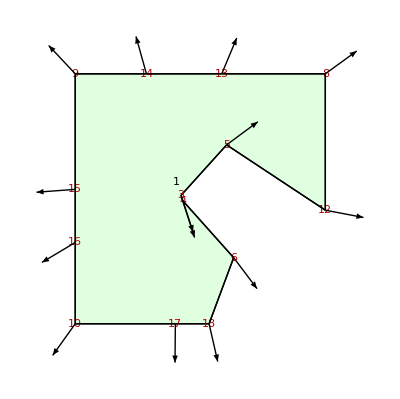

```mathematica
len = .5 * EdgeLengths[TPrime]//Mean
Show[cellmap,Graphics[MapThread[Arrow[{#1,#1+len*#2}]&, {CVC, COV}]]]
```